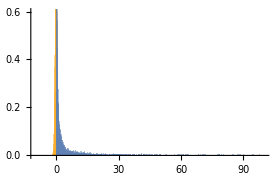

```mathematica
(* Brownian Motion and Levy Flights *)

dataL=RandomVariate[LevyDistribution[0,0.5],10000];
dataL=DeleteCases[dataL,x_/;x>100];
dataR=RandomVariate[NormalDistribution[0,0.5],10000];
Show[Histogram[{dataR,dataL},1000,"ProbabilityDensity",PlotRange->{{-10,100},{0.00,0.6}}]] (* ScalingFunctions->{"lin","log"} *)
```

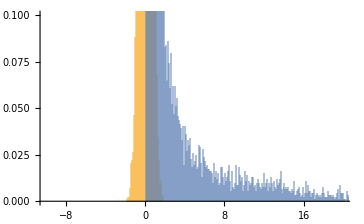

```mathematica
Show[Histogram[{dataR,dataL},1000,"ProbabilityDensity",PlotRange->{{-10,20},{0.00,0.1}}]]
```

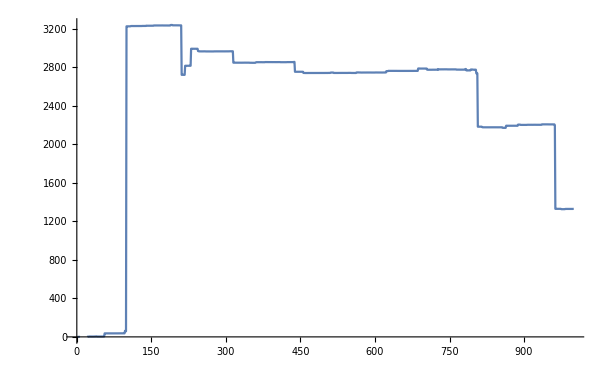

```mathematica
dL=RandomVariate[LevyDistribution[0.001,0.005],1000];
dLs=2*(RandomInteger[1,1000]-0.5);
dL=dL*dLs;
dR=100*RandomVariate[NormalDistribution[0,0.5],1000];
dLa=Accumulate[dL];
dRa=Accumulate[dR];
ListLinePlot[dLa]
```

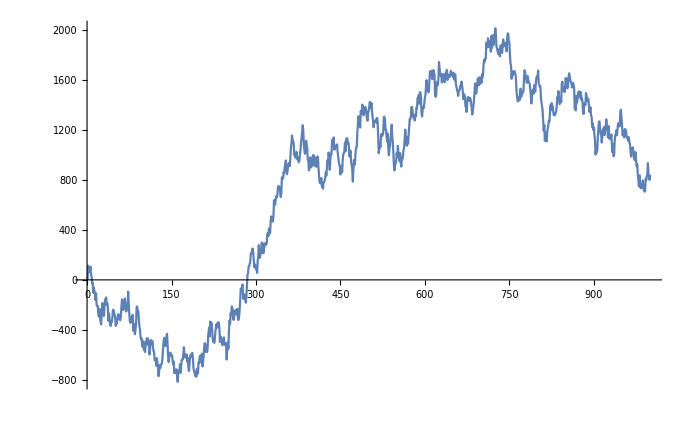

```mathematica
ListLinePlot[dRa]
```

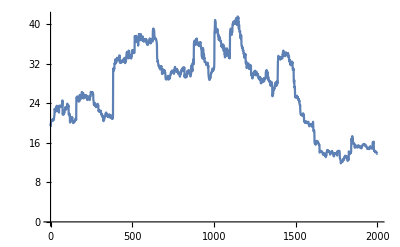

```mathematica
dLogReturn=RandomVariate[StableDistribution[1,1.38,-0.096,-0.001,0.005],2000];
dLa=20*Exp[Accumulate[dLogReturn]];
ListLinePlot[dLa]
```

```mathematica
(* Assuming stock logarithmic return follows a stable distribution,find the value at risk at the 95% level: *)
```

```mathematica
logD=StableDistribution[1,1.38,-0.096,-0.001,0.005];
VaR=InverseSurvivalFunction[logD,0.95]
```

-0.0186983

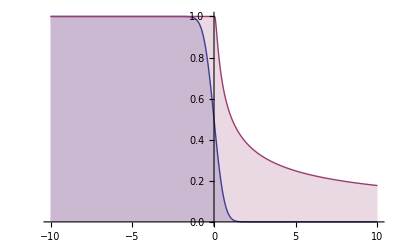

```mathematica
su1=SurvivalFunction[NormalDistribution[0,0.5]];
su2=SurvivalFunction[LevyDistribution[0,0.5]];
Plot[{su1[x],su2[x]},{x,-10,10},Filling->Axis]
```

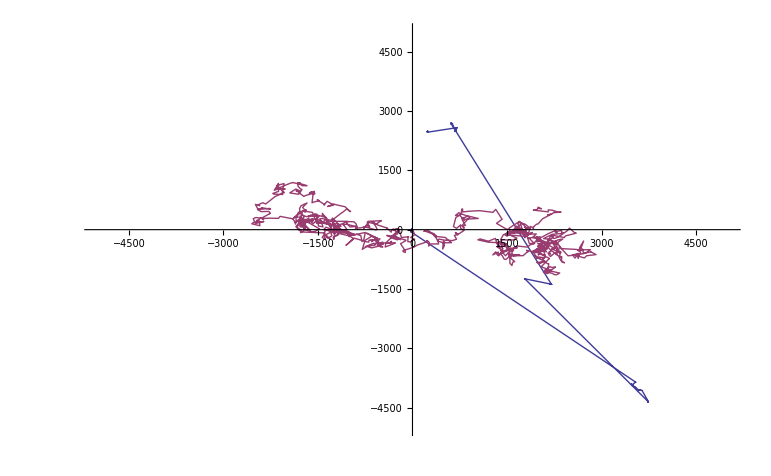

```mathematica
NN=1000;
dLx=RandomVariate[LevyDistribution[0.0,0.005],NN];
dLx1=RandomVariate[NormalDistribution[0.0,100],NN];
dLP=RandomReal[{0,2*Pi},NN];
dLP1=RandomReal[{0,2*Pi},NN];
x={0};y={0};x1={0};y1={0};
For[j=0,j<NN,j++;dr=dLx[[j]]*Exp[I*dLP[[j]]];AppendTo[x,x[[j]]+Re[dr]];AppendTo[y,y[[j]]+Im[dr]]];
For[j=0,j<NN,j++;dr=dLx1[[j]]*Exp[I*dLP1[[j]]];AppendTo[x1,x1[[j]]+Re[dr]];AppendTo[y1,y1[[j]]+Im[dr]]];
ListLinePlot[{Transpose[{x,y}],Transpose[{x1,y1}]},PlotRange->{{-5000,+5000},{-5000,5000}}]
```

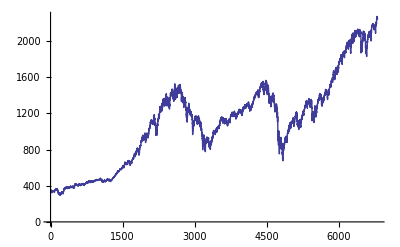

```mathematica
closingValues=FinancialData["SP500","Close","Jan 1., 1990","Value"];
ListLinePlot[closingValues]
```

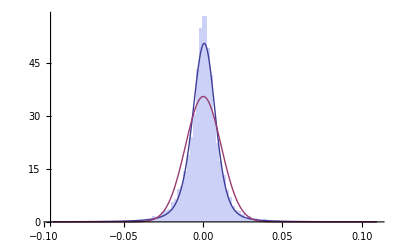

```mathematica
logr=Differences[Log[closingValues]];
edist1=EstimatedDistribution[logr,StableDistribution[1,α,β,μ,σ]];
edist2=EstimatedDistribution[logr,StableDistribution[1,2,0,μ1,σ1]]; (* Gauss *)
Show[Histogram[logr,Automatic,"PDF"],Plot[{PDF[edist1,x],PDF[edist2,x]},{x,Min[logr],Max[logr]},PlotRange->All,PlotStyle->Thick]]
```

```mathematica
edist1
```

StableDistribution[1,1.57582,-0.137138,0.000108547,0.00566342]

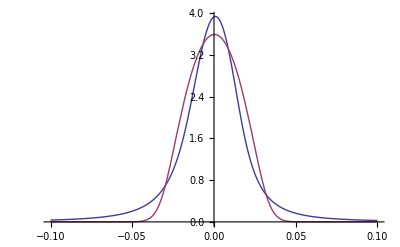

```mathematica
f1[x_]:=Log[1+PDF[edist1,x]];
f2[x_]:=Log[1+PDF[edist2,x]];

Plot[{f1[x],f2[x]},{x,-0.1,+0.1},PlotStyle->Thick]
```

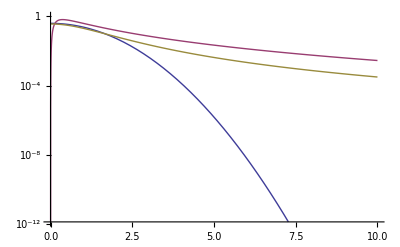

```mathematica
LogPlot[{PDF[NormalDistribution[0,1],x],PDF[LogNormalDistribution[0,1],x],PDF[StudentTDistribution[0,1,3],x]},{x,0,+10},PlotStyle->Thick]
```

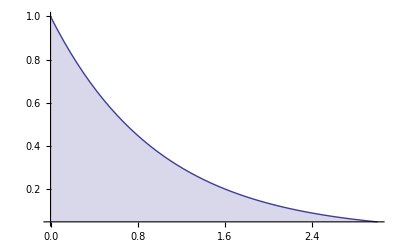

```mathematica
Plot[PDF[ExponentialDistribution[1],x],{x,0,3},Filling->Axis,PlotRange->All]
```

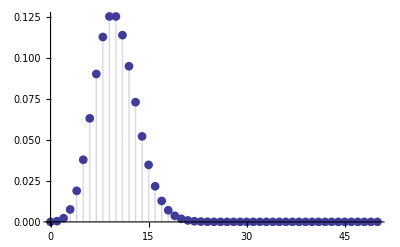

```mathematica
DiscretePlot[PDF[PoissonDistribution[1*10],x],{x,0,50},PlotMarkers->Automatic,PlotRange->All]
```

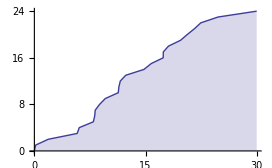

```mathematica
dP=RandomFunction[PoissonProcess[1],{0,30}];
ListLinePlot[dP,Filling->Axis]
```

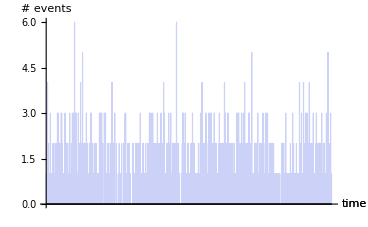

```mathematica
tab=Table[RandomVariate[PoissonDistribution[1]],{1000}];
BarChart[tab,AxesLabel->{time, "# events"}]
```

```mathematica
Table[CorrelationFunction[tab,n],{n,2,10}]//N
```

{0.031993,-0.00640544,0.0205037,0.000452692,-0.000507255,0.03789,0.0157765,0.0282714,0.0244094}